## Utility

```mathematica
Labels[type_] := SortBy[StringDrop[StringSplit[#,"/"][[-1]],Switch[type,"m",-2,_,-3]]&/@FileNames[NotebookDirectory[]<>"/"<>type<>"/*."<>type],{Cutoff[#],U[#],J[#],NSites[#]}&];
Job[label_] := StringSplit[label,"_"][[1]];
BC[label_] := StringSplit[label,"_"][[2]];
NSites[label_] := ToExpression[StringSplit[label,"_"][[3]]];
MaxDim[label_] := ToExpression[StringSplit[label,"_"][[4]]];
Cutoff[label_] := StringSplit[label,"_"][[5]];
Prec[label_] := StringSplit[label,"_"][[6]];
J[label_] := StringSplit[label,"_"][[7]];
U[label_] := ToExpression[StringSplit[label,"_"][[8]]];
Charge[label_] := ToExpression[StringSplit[label,"_"][[9]]];
ReadData[label_,type_] := Module[{stream, str},
stream = OpenRead[NotebookDirectory[]<>"/"<>type<>"/"<>label<>"."<>type];
str = ReadString[stream];
Close[stream];
str = StringReplace[str,"e"->"*10^"];
If[type!="m"&&type≠"an",
str = "{" <> StringDrop[StringReplace[StringReplace[str,"\n"->""],",}"->"}"],-1]<> "}"//ToExpression
];
str//ToExpression
];
FitParameterWithError[parameter_] := Module[{ndig = -Floor[Log10[parameter[[2]]]]},
ToString[SetAccuracy[parameter[[1]],ndig+1]]<>"("<>ToString[Round[10^ndig*parameter[[2]]]]<>")"
];
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->14};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
```

## Analysis

### Central charge from entanglement entropy

```mathematica
AnalyzeEE[name_] := Module[{len,Y,X,L,lm,c,A,x},
Y = ReadData[name,"ee"] ;
len = Length[Y];
X = Y[[-1]];
L = NSites[name]-If[BC[name]=="p",0,1];
X = Select[X, L/5<#[[1]]<L*4/5&];
If[BC[name]=="p",
lm = LinearModelFit[X,Log[L/π Sin[π x/L]]/3 ,x];,
If[job=="haagerup",X=Select[X,Mod[#[[1]],period]!=2&]];
lm = LinearModelFit[X,Log[L/π Sin[π (x-1/2)/L]]/6 ,x];
];
c = FitParameterWithError[lm["ParameterTableEntries"][[2]]];Show[ListPlot[#&/@Y,AxesLabel->{MaTeX["\\ell",Magnification->1.5],MaTeX["S_\\ell",Magnification->1.5]},PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[BC[name]=="p","Periodic","Open"]<>"  } L="<>ToString[NSites[name]] <> "~~c="<>c<>" \\end{array}",Magnification->1.5]
,PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[{lm[x]},{x,0,L}]]
];
```

### Scaling dimension from energy

```mathematica
fitGSEnergy[gsEnergies_,minL_,bc_,show_] := Module[{maxL,min,max,minE,maxE,GSEnergy,Energy},
lm = LinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],{L,1,1/L,1/L^2},L];
maxL = Max[Transpose[gsEnergies][[1]]]*1.01;
min = SortBy[gsEnergies,#[[2]]/#[[1]]&][[2]];
max = SortBy[gsEnergies,#[[2]]/#[[1]]&][[-2]];
minE = Floor[100*min[[2]]/min[[1]]]/100;
maxE = Ceiling[100*max[[2]]/max[[1]]]/100;
plot = Show[
ListPlot[{#[[1]],#[[2]]/#[[1]]}&/@gsEnergies,Joined->False,
PlotLabel->MaTeX["\\text{\\bf "<>If[bc==="p","Periodic","Open"]<>"}",Magnification->1.5],
AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["E_1/L",Magnification->1.5]},PlotRange->{{0,maxL},{minE,maxE}},AxesOrigin->{0,Min[minE,0]}
],
Plot[lm[L]/L,{L,0,maxL}]
];
If[show,
Print[lm["ParameterTable"]];
Print[plot];
];
GSEnergy[L0_] := lm[L0];
Energy[L0_,E0_] := (E0-GSEnergy[L0])/(-lm["ParameterTableEntries"][[3,1]])*L0/If[bc=="p",12,24];
Energy
];
```

### Periodic spectral analysis

```mathematica
tol = 2*10^-2;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,Black,Black};
markers = {"●","○","○"};
height = 2.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
plots = Table[ListPlot[{#[[1]],#[[2]]*c}&/@spectrumByRho[[i]],PlotMarkers->{markers[[i]],8},PlotStyle->styles[[i]]],{i,1,3}];
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{0,0},PlotRange->{{-L/2,L/2},{0,height}},AxesLabel->{MaTeX["p",Magnification->1.5],MaTeX["\\Delta",Magnification->1.5]},ImageSize->{Automatic,200},AspectRatio->height/L]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
]
```

### Open spectral analysis

```mathematica
tol = 1*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],(*Length[#]==3&&*)Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,Black,Black,Black,Black};
markers = {"●","○","○","○","○"};
height = 3;
OpenSpectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{data,L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
data = Table[{i-1,#[[2]]*c}&/@spectrumByRho[[i]],{i,1,Length[rs]+1}];
data = DeleteCases[data,{}];
plots = {ListPlot[data,PlotMarkers->({#,9}&/@markers),PlotStyle->styles,Ticks->{{{0,MaTeX["\\text{I}",Magnification->1.5],0},{1,MaTeX["\\text{II}",Magnification->1.5],0},{2,MaTeX["\\text{III}",Magnification->1.5],0},{3,MaTeX["\\text{IV}",Magnification->1.5],0}}[[1;;Length[rs]]],Automatic}]};
Do[
AppendTo[plots, Plot[spectrumByRho[[i,1,2]]*c+If[i==1,2,1],{x,i-1-0.05,i-1+0.05},PlotStyle->{{Black}}]];
,{i,1,Length[rs]}
];
If[Mod[L,period]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,0,3}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{-.5,0},PlotRange->{{-.5,Length[rs]+.25},{0,height}},AxesLabel->{"",MaTeX["\\Delta",Magnification->1.5]},ImageSize->{Automatic,300},AspectRatio->1]
];

OpenSpectrumIncludingFit[L0_,j_,q_,cutoff_] := Module[{},
spectra = {NSites[#]-1,ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,minL,"d",False];
spectra = {NSites[#]-1,ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
OpenSpectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
]
```

## Haagerup

### Global variables

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
{job,bc,maxdim,cutoff,j,u,q} = {"haagerup","d",1600,"1e-08","1,-1,0",2,0};
rs = If[bc=="p",{ζ,-1/ζ},{1,-0.322,-0.535,0.554}];
cc = 2;
minL = 6;
```

### Dynamical exponent

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,1]]-#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
maxL = Max[Transpose[gaps][[1]]];
gaps = Select[gaps,#[[1]]≥maxL/2&];
logGaps = {Log[#[[1]]],Log[#[[2]]]}&/@gaps;
lm = LinearModelFit[{#[[1]],#[[2]]}&/@logGaps,L,L];
c = FitParameterWithError[lm["ParameterTableEntries"][[1]]];
z = FitParameterWithError[lm["ParameterTableEntries"][[2]]];
```

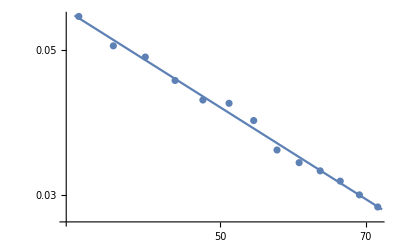

```mathematica
plot = Show[
ListLogLogPlot[gaps,AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\Delta E",Magnification->1.5]},
PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[bc=="p","Periodic","Open"]<>"} \\\\ \\log(\\Delta E) = "<>z<>" \\log(L) + "<>c<>" \\end{array}",Magnification->1.5]],
Plot[lm[L],{L,Log[maxL/2]-0.01,Log[maxL]+0.01}]
]
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/puredyn.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/puredynOpen.pdf",plot];
```

### Central charge from entanglement entropy

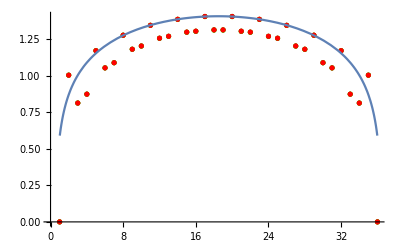

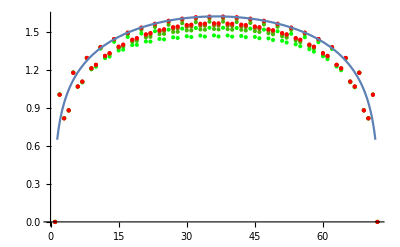

```mathematica
plots = AnalyzeEE[#]&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&&IntegerQ[(NSites[#]-If[BC[#]=="p",0,1])/If[BC[#]=="p",18,36]]&];
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/ee18.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/ee36.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen36.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen72.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen36Alt.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen72Alt.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/ee18_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/ee36_1,-1,0.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen36_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen72_1,-1,0.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen36Alt_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/eeOpen72Alt_1,-1,0.pdf",plots[[2]]];
```

### Scaling dimension from energy

| Estimate | Standard Error | t-Statistic | P-Value
L | -0.823475 | 1.09426×10^-6 | -752543. | 5.63535×10^-101
1 | 0.529774 | 0.0000868068 | 6102.9 | 3.01869×10^-61
1/L | -0.26708 | 0.00168713 | -158.305 | 4.08914×10^-31
1/L^2 | 0.32057 | 0.00790216 | 40.5675 | 6.37567×10^-20

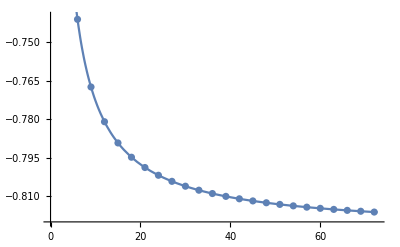

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
Energy = fitGSEnergy[gsEnergies,minL,bc,True];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energyOpen.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy_1,-1,0.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energyOpen_1,-1,0.pdf",plot];
```

### Periodic spectral analysis

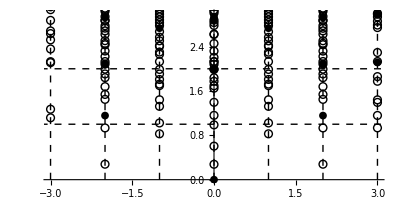

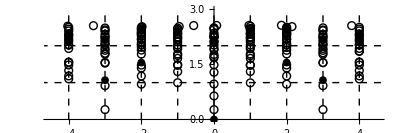

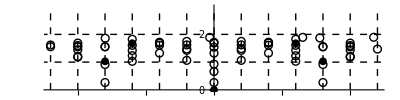

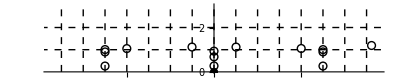

```mathematica
If[bc!="p",
Print["Change bc"];
,
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,6,15,period}]//Flatten;
Print[#]&/@plots;
]
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec6.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec9.pdf",plots[[2]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec12.pdf",plots[[3]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec15.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec6_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec9_1,-1,0.pdf",plots[[2]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec12_1,-1,0.pdf",plots[[3]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec15_1,-1,0.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq6.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq9.pdf",plots[[2]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq12.pdf",plots[[3]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq15.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec8.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec11.pdf",plots[[2]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec14.pdf",plots[[3]]];
```

### Open spectral analysis

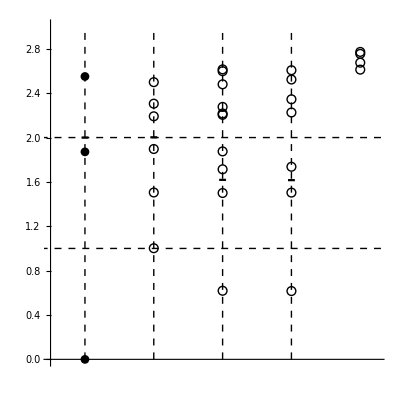

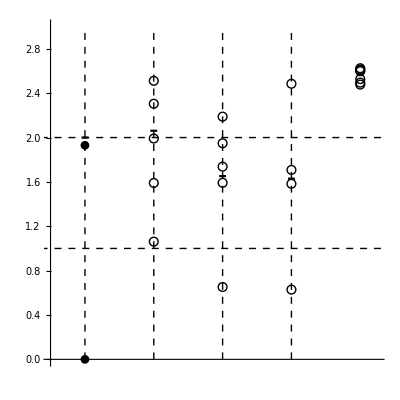

```mathematica
If[bc=="p",
Print["Change bc"];
,
plots = Table[OpenSpectrumIncludingFit[L0,j,q,"1e-08"],{L0,18,30,12}]//Flatten;
Print[#]&/@plots;
]
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specOpen18.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specOpen30.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specOpen18_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specOpen30_1,-1,0.pdf",plots[[2]]];
```

### Open spectral analysis: Diagnose L=36 problem

```mathematica
spectra = {NSites[#]-1,ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,minL,"d",False];
```

```mathematica
2*Energy[36,#]&/@Transpose[Select[spectra,#[[1]]==36&][[1,2]]][[2]]//Sort
```

{0.000172664,0.644846,0.646682,1.07667,1.59511,1.61243,1.61803,1.74928,1.80242,1.93976,1.98341,2.02813,2.24458,2.35634,2.50828,2.51761,2.59845,2.62082,2.62356,2.62881,2.63182}

```mathematica
spectra = {NSites[#]-1,ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
```

```mathematica
2*CollectByRho[Energy,Spec[36]]//MatrixForm
```

({{1.99932,0.00091652},{1.99948,1.73092}}
{{-0.643956,1.07681},{-0.644034,1.61429},{-0.643576,2.00115}}
{{-1.07,0.655024},{-1.0699,1.58454},{-1.06944,1.7526},{-1.0698,1.89223},{-1.06938,2.17903}}
{{1.10856,0.654679},{1.10868,1.55301},{1.10726,1.7466}}
{{-0.661728,2.42909},{-1.05662,2.51304},{-0.415748,2.55064},{0.704494,2.55388},{1.1651,2.58943},{-0.93976,2.60635},{-0.313054,2.60703}})

## Golden

### Global variables

```mathematica
period = 2;
ζ = (1+Sqrt[5])/2;
{job,bc,maxdim,cutoff,j,u,q} = {"golden","d",1600,"1e-08","-1",2,0};
rs = If[bc=="p",{ζ,-1/ζ},{-1/ζ,1/ζ^2}];
cc = 0.7;
minL = 6;
```

### Dynamical exponent

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,1]]-#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
maxL = Max[Transpose[gaps][[1]]];
gaps = Select[gaps,#[[1]]≥maxL/2&];
logGaps = {Log[#[[1]]],Log[#[[2]]]}&/@gaps;
lm = LinearModelFit[{#[[1]],#[[2]]}&/@logGaps,L,L];
c = FitParameterWithError[lm["ParameterTableEntries"][[1]]];
z = FitParameterWithError[lm["ParameterTableEntries"][[2]]];
```

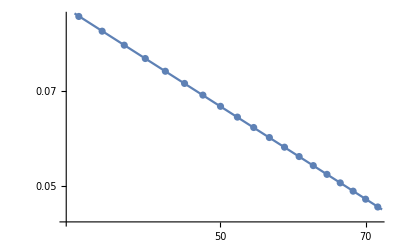

```mathematica
plot = Show[
ListLogLogPlot[gaps,AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\Delta E",Magnification->1.5]},
PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[bc=="p","Periodic","Open"]<>"} \\\\ \\log(\\Delta E) = "<>z<>" \\log(L) + "<>c<>" \\end{array}",Magnification->1.5]],
Plot[lm[L],{L,Log[maxL/2]-0.01,Log[maxL]+0.01}]
]
```

### Central charge from entanglement entropy

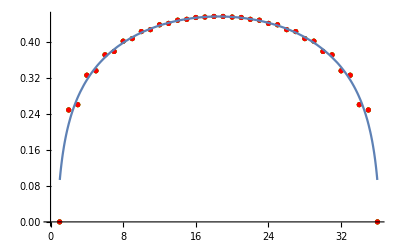

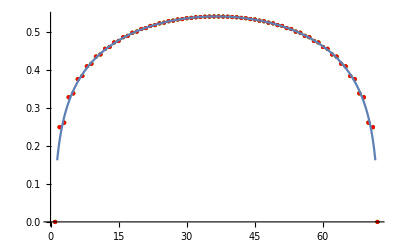

```mathematica
plots = AnalyzeEE[#]&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&&IntegerQ[(NSites[#]-If[BC[#]=="p",0,1])/If[BC[#]=="p",18,36]]&];
Print[#]&/@plots;
```

### Scaling dimension from energy

| Estimate | Standard Error | t-Statistic | P-Value
L | -0.76393 | 2.00916×10^-7 | -3.80223×10^6 | 8.23037×10^-177
1 | 0.580046 | 0.0000159581 | 36348.1 | 3.17789×10^-116
1/L | -0.157149 | 0.000313724 | -500.914 | 2.10343×10^-60
1/L^2 | 0.136142 | 0.00151539 | 89.8398 | 4.88772×10^-38

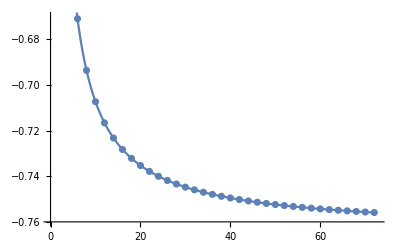

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
Energy = fitGSEnergy[gsEnergies,minL,bc,True];
```

### Periodic spectral analysis

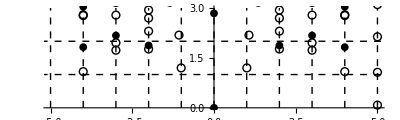

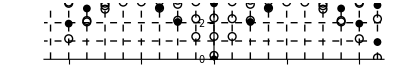

```mathematica
If[bc!="p",
Print["Change bc"];
,
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,10,18,8}]//Flatten;
Print[#]&/@plots;
]
```

### Open spectral analysis

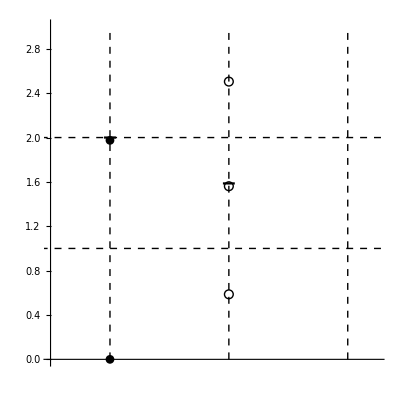

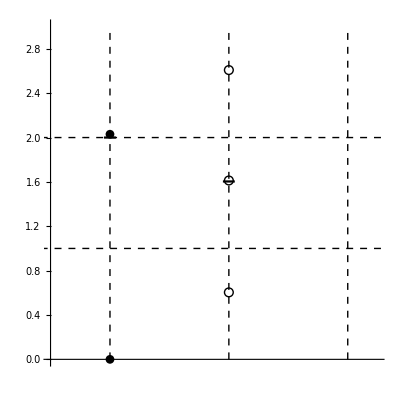

```mathematica
If[bc=="p",
Print["Change bc"];
,
plots = Table[OpenSpectrumIncludingFit[L0,j,q,"1e-08"],{L0,18,30,12}]//Flatten;
Print[#]&/@plots;
]
```